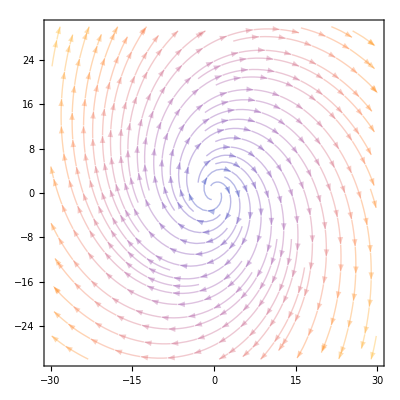
{{(1 | 2
-3 | 1),{x+2 y,-3 x+y},{div,2,2,2},{curl,-5,-5}}
-Graphics-}

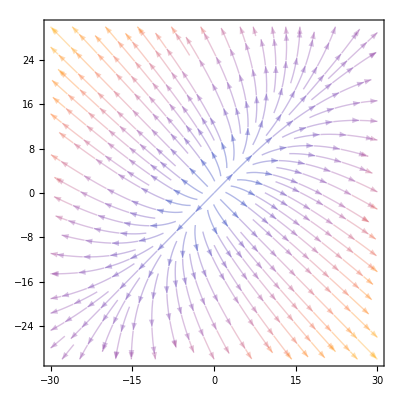
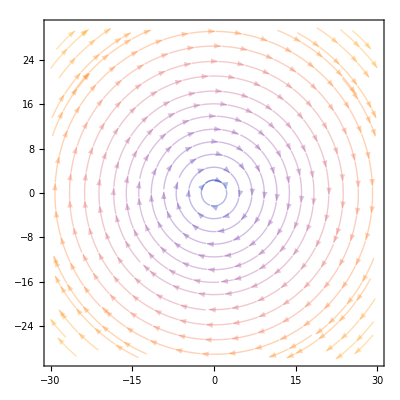
{{{{(1. | -0.5
-0.5 | 1.),{1. x-0.5 y,-0.5 x+1. y},{div,2.,2.,2.},{curl,0.,0.}}
-Graphics-},{{(0. | 2.5
-2.5 | 0.),{0.+2.5 y,0.-2.5 x},{div,0,0.,0.},{curl,-5.,-5.}}
-Graphics-}}}

```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
PlotMatrixDivCurl[M_]:=Module[
{a,b,c,d,MM,fn,div,div1,div2,curl,curl1,start,end,len},
{
MM=M;
({{a, b}, {c, d}})=M;

(*构造矢量场 MM（x,y）这种向量场所有的点旋度相等，所有点散度相等*)
fn={u,v}=MM.{x,y};


div=Div[{u,v},{x,y}]//Simplify;
curl=Curl[{u,v},{x,y}]//Simplify;

(*矩阵的迹就是 MM.{x,y} 向量场的散度*)
div1=Tr[MM];
div2=a+d;
(*二维矩阵的斜对角线之差就是向量场的旋度*)
curl1=c-b;

start=-30;end=-start;len=end;

{
{MM//MatrixForm,fn,{"div",div,div1,div2},{"curl",curl,curl1}},
Show[
{

StreamPlot[fn,{x,start,end},{y,start,end},StreamStyle->{Opacity[0.3]}](*,
VectorPlot[fn,{x,start,end},{y,start,end},VectorStyle->Opacity[0.1]]*)
}]
}//Column
}];
DecomposeMatrixDivCurl[M_]:=Module[
{a,b,c,d,a1,b1,c1,d1,a2,b2,c2,d2,mm1,mm2,result},

{

(*分解成 对称矩阵 无旋+ 反对称矩阵 无散*)
mm1=((M+Transpose[M])/2.);

mm2=((M-Transpose[M])/2.);

{
PlotMatrixDivCurl[mm1],
PlotMatrixDivCurl[mm2]
}
}]


MM=({{1, 2}, {-3, 1}});

PlotMatrixDivCurl[MM]
DecomposeMatrixDivCurl[MM]
```

```mathematica
(* 无旋有散场  ({{a, c}, {c, b}})*) 
Manipulate[
PlotMatrixDivCurl[({{a, c}, {c, b}})],
{{a,1},-10,10},
{{b,2},-10,10},
{{c,1},-10,10}
]
```

```mathematica
(* 无散有旋场   ({{a, b}, {c, -a}})*) 
MM=({{1, 3}, {2, -1}});
PlotMatrixDivCurl[MM]
```

```mathematica
(* 无散无旋场   ({{a, c}, {c, -a}})*) 
MM=({{1, 3}, {3, -1}});
PlotMatrixDivCurl[MM]
```